```mathematica
Nt = 4000;
ti = 0; tf = 14; (*5*)
deltat = (tf - ti) /Nt ;
Nx =60; (*455*)
(*xi = -2; xf = 8;*)
xi = 0; xf = 60; (*-40 to 40*)
deltax = (xf - xi) / Nx;
c =  1;
r = c * (deltat / deltax)//N
deltat//N
deltax//N
```

0.0035

0.0035

1.

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
```

```mathematica
T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1}],32];

(*For Perodic Interpolation*) 
Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

X= N[Table[xm = xi + m *deltax, {m, 0, Nx - 1}],32];

f[x_] = If[1 ≤ x ≤59 ,400,0];
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrices*)
(************************************************************************************************************************)
```

```mathematica
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->1]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],X, "DifferenceOrder"->2]@"DifferentiationMatrix"//Normal), {i,1,3}],32];
DL2 = N[Table[(-c)^i * L2[[i]] * (deltat)^i,{i,1,3}],32];

DL2 = (-c) * (deltat)* (NDSolve`FiniteDifferenceDerivative[2,X, "DifferenceOrder"->2]@"DifferentiationMatrix"//Normal);
```

```mathematica
(*LD2*)
ULD2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
ULD2[[1,All]] = N[f[X],32];
ULD2 = Chop[ULD2, 10^(-307)];
ULD2 = Developer`ToPackedArray[ULD2, Real]; 
Developer`PackedArrayQ[ULD2]


ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - ((DL2 / 2)),32];
BLD2 = N[ILD2 + ((DL2 / 2)),32];
MLD2 = N[Inverse[ALD2].BLD2,32];
EMLD2 = N[MLD2 - ILD2,32];
EMLD2 = Developer`ToPackedArray[EMLD2, Real]; 

Do[
ULD2[[n+1,All]] = ULD2[[n,All]] + (EMLD2).ULD2[[n,All]];
ULD2[[n + 1,1]] = 0; (*Boundary Cond*)
ULD2[[n + 1, -1]] = 0;
, {n,1,Nt - 1 }];
Do[ULD2[[-1,m+1]] = 0,{m,1,Nx-1}];
ULD2[[1,-1]] = 0;(* why does this point keep becoming 400 instead of 0?*)(*Should this be a Boundary Cond?*)
```

True

```mathematica
(*Partial Inversion Order 2*)
UP= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UP[[1,All]] = N[f[X],32];
UP = Chop[UP, 10^(-307)];
UP = Developer`ToPackedArray[UP, Real]; 
Developer`PackedArrayQ[UP]

selectwidth = 8;

(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(*Grid if you use the PeriodicInterpolation command when creating the L Matrix*)
(*grid=x0+(Range[totalpoints + 1]-middlepoint)Δx;*)

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[2],grid,"DifferenceOrder"->2]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
(*This is done so the M Matrix can be created symbollically and be created for any CFL Number by putting in a value for r*)
r=.;
LPX = LP*((-c))*(r*(Δx)^2);

(*LPX = LPX//.{r -> (deltat / (deltax)^2)};*)

(*Set up Identity Matrix*)
IP=IdentityMatrix[Length[LPX]];

(*Generate a Crank–Nicolson M Matrix for the stencil*)
(Mn=Inverse[IP-LPX/2 ].(IP+LPX/2));

(*Take the middle row from this Crank-Nicolson M Matrix*)
fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,0,Nx-1},{j,0,Nx-1}];

MP = MP//.{r -> (deltat / (deltax)^2)};

Ip = IdentityMatrix[Length[MP]];

EMP = MP - Ip;

EMP= Developer`ToPackedArray[EMP, Real]; 

Do[
UP[[n+1,All]] = UP[[n,All]] + (EMP).UP[[n,All]];
UP[[n + 1,1]] = 0; (*Boundary Cond*)
UP[[n + 1, -1]] = 0;
, {n,1,Nt - 1 }];
Do[UP[[-1,m+1]] = 0,{m,1,Nx-1}];
UP[[1,-1]] = 0;
```

True

```mathematica
(*Don't need the Differentiation Matrices to have 32 digits anymore*)
{{L1 = Developer`ToPackedArray[L1, Real]; 
L2 = Developer`ToPackedArray[L2, Real];}, {}}
```

{{Null^2},{Null}}

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*LD2*)
FLD2 = Table[0,{i,1,Nt},{j,1,Nx}];
FLD2 = Developer`ToPackedArray[FLD2, Real];
intLD2 = Table[0,{i,1,Length[FLD2[[All,1]]]}];
intLD2 = Developer`ToPackedArray[intLD2, Real];
Do[
FLD2[[i,All]] = (L2[[1]].ULD2[[i,All]])^2;

intLD2[[i]] = (xf - xi)/Nx Total[FLD2[[i,All]]]
,{i,1,Length[FLD2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intCN}]},Joined->True]*)
```

```mathematica
(*Partial Inversion Order 2*)
FP = Table[0,{i,1,Nt},{j,1,Nx}];
FP = Developer`ToPackedArray[FP, Real];
intP = Table[0,{i,1,Length[FP[[All,1]]]}];
intP = Developer`ToPackedArray[intP, Real];
Do[
FP[[i]] = (L2[[1]].UP[[i,All]])^2;

intP[[i]] = (xf-xi)/Nx Total[FP[[i,All]]]
,{i,1,Length[FP[[All,1]]]}];
```

```mathematica
energyErrorLD2 = Abs[intLD2 - intLD2[[1]]];
energyErrorP = Abs[intP - intP[[1]]];
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

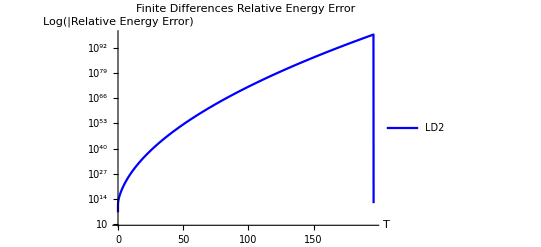

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}] Transpose[{T,energyErrorP}]},PlotStyle->{Blue, Red,Green, Orange,Pink,Yellow,Gray, LightBlue, LightRed},PlotLegends->{"LD2","LD4","RK2","RK4","LD6","RK6","LD8", "PI2", "PI4"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Finite Differences Relative Energy Error",Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4, energyErrorLD6,energyErrorRK6,energyErrorLD8}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FD_Energy_Error_Final_Test_50.dat",exportData,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*L1 Error*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*LD2*)
abserrLD2 = Abs[ULD2-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}]]*)
```

```mathematica
(*Partial Inversion Order 2*)
abserrP = Abs[UP-Uexact];
errorP = Table[0,{i,1,Length[abserrP]}];
errorP = Developer`ToPackedArray[errorP, Real];
Do[
errorP[[i]] = Norm[abserrP[[i,All]], 1] * deltax;
,{i,1,Length[errorP]}
];
```

```mathematica
(*ListLogPlot[{Transpose[{T,errorLD2}], Transpose[{T,errorP}]},PlotRange->{{ti,tf},{10^(-14),10^(0)}}, PlotStyle->{{Blue,Dashed},{Green,Opacity[0.5]},{Red,Dashed},{Orange,Opacity[0.5]},{Pink,Dashed},{Yellow,Opacity[0.5]},Gray,LightBlue, LightRed},PlotLabel->"Finite Differences L1 Error",PlotLegends->{"LD2","RK2","LD4","RK4","LD6","RK6","LD8","PI2", "PI4"},AxesLabel->{"T","Log(|Relative Energy Error|)"},Joined->True]*)
```

```mathematica
(*exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4,errorLD6,errorRK6,errorLD8}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FD_Error_Final_Test_50.dat",exportData,"Table"];*)
```

```mathematica
(*Animate[ListPlot[Table[UN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
aniLD2 = Animate[ListPlot[{Table[UP[[n+1, m+1]], {m,0,Nx-1}],Table[ULD2[[n+1, m+1]], {m,0,Nx-1}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{All,{0,400}}], {n,0,Nt -1,1} ,AnimationRunning->False]
```

```mathematica
(*Animate[ListLinePlot[Transpose[{X,Abs[UCN[[n]] - Uexact[[n]]]}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]*)
```